# Checking trafo1Namps-to-helicity.f against 1N amplitude constructed in deuteron onebody notebook

## Enter subtitle here

Enter subsubtitle here

<very short description>
Version X.x, hgrie DATE  (Short Description, Version History) (nothing to execute)

This notebook produces <very short description>

Underlying manu-script: <main reference>

## Version History and To Do List

### To Do

### Changes in vX.x DATE

## Comments (nothing to execute)

### Explaining Parameters, Conventions

All angles θ are in _XXX_!

### Explanation of observables and kinematics

### Variable Names

### Comments on Fit Procedures

## 0. Preparations + Startup, hgrie: Internal definitions, do not change. MUST BE EXECUTED WHEN LOADING .mx FILE!

## This Notebook’s Styles

Note hgrie July 2017 : 
 This notebook feels and smells like the StandardReport.nb style, but it is actually the Default.nb with a few tweaks. 
  Amongst other things, I get around the annoying problems with gray colours in StandardReport.nb.

```mathematica
SetOptions[EvaluationNotebook[],
CodeAssistOptions->{"FloatingElementEnable"->False},
StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],
Cell[StyleData["Notebook"],Background->RGBColor[1,0.96,0.90]],
Cell[StyleData["Title"],CellMargins->{{20(*left*),Inherited(*right*)},{0(*bottom*),7(*top*)}}],
Cell[StyleData["Subtitle"],CellMargins->{{40(*left*),Inherited(*right*)},{0(*bottom*),7(*top*)}}],
Cell[StyleData["Subsubtitle"],CellMargins->{{40(*left*),Inherited(*right*)},{0(*bottom*),7(*top*)}}],
Cell[StyleData["Chapter"],FontSize->24,CellFrame->{{0,0},{0,5}},CellMargins->{{20(*left*),Inherited(*right*)},{0(*bottom*),5(*top*)}}],
Cell[StyleData["Subchapter"],FontSize->24,CellFrame->{{0,0},{0,3}},ShowGroupOpener->True,CellDingbat->None,CellMargins->{{40(*left*),Inherited(*right*)},{0(*bottom*),5(*top*)}}],
Cell[StyleData["Section"],FontSize->24,CellFrame->{{0,0},{0,2}},CellFrameColor->RGBColor[0,0,0.5],ShowGroupOpener->True,CellMargins->{{50(*left*),Inherited(*right*)},{7(*bottom*),5(*top*)}}],
Cell[StyleData["Subsection"],ShowGroupOpener->True,CellMargins->{{60(*left*),Inherited(*right*)},{0(*bottom*),5(*top*)}}],
Cell[StyleData["Subsubsection"],ShowGroupOpener->True,CellMargins->{{70(*left*),Inherited(*right*)},{0(*bottom*),5(*top*)}}],
Cell[StyleData["Text"],CellMargins->{{70(*left*),Inherited(*right*)},{5(*bottom*),5(*top*)}}],
Cell[StyleData["Item"],MenuCommandKey->"*",CellMargins->{{80(*left*),Inherited(*right*)},{5(*bottom*),5(*top*)}}],
Cell[StyleData["Subitem"],CellMargins->{{90(*left*),Inherited(*right*)},{5(*bottom*),5(*top*)}}],
Cell[StyleData["Subsubitem"],CellMargins->{{100(*left*),Inherited(*right*)},{5(*bottom*),5(*top*)}}],
Cell[StyleData["ItemNumbered"],MenuCommandKey->"+",CellMargins->{{80(*left*),Inherited(*right*)},{5(*bottom*),5(*top*)}}],
Cell[StyleData["DisplayFormula"],MenuCommandKey->"(",Background->White,CellMargins->{{70(*left*),Inherited(*right*)},{5(*bottom*),5(*top*)}}],
Cell[StyleData["DisplayFormulaNumbered"],MenuCommandKey->")",Background->White,CellMargins->{{70(*left*),Inherited(*right*)},{5(*bottom*),5(*top*)}}],
Cell[StyleData["Input"],CellFrame->{{1,1},{0,1}},CellMargins->{{70(*left*),Inherited(*right*)},{0(*bottom*),7(*top*)}},Background->RGBColor[0.87,0.94,1]],
Cell[StyleData["Output"],CellFrame->{{1,1},{1,0}},CellMargins->{{70(*left*),Inherited(*right*)},{Inherited(*bottom*),0(*top*)}},Background->GrayLevel[1]],
Cell[StyleData["Code"](*mathematica code*),MenuCommandKey->"!",CellMargins->{{70(*left*),Inherited(*right*)},{Inherited(*bottom*),10(*top*)}},Background->Yellow],
Cell[StyleData["Program"](*generic programming code*),MenuCommandKey->"@",CellMargins->{{70(*left*),Inherited(*right*)},{Inherited(*bottom*),10(*top*)}},Background->RGBColor[100/255,149/255,237/255]],
Cell[StyleData["InitializationCell"],MenuCommandKey->"#",CellMargins->{{70(*left*),Inherited(*right*)},{Inherited(*bottom*),10(*top*)}},Background->Green]}(*,StyleDefinitions->"PrivateStylesheetFormatting.nb"*)]]
```

## Set version number of this file

```mathematica
fileversion=StringForm["v1.0"];
```

## Comments: How To Do Things

#### How To Print/Save as .pdf Over-Wide Stuff (comments only)

select cells
right-click, choose “print selection”
-> “print to pdf
	-> Options
		page size ->A2, or even A1
		Landscape
	print
Open printed file with acroread
	screenshot/select desired area
	right-click, choose “print”	
Done.

#### Stylesheet manipulations (comments only)

The following for notebook stylesheet StandardReport, to make plotmarks not have gray background:

Format->Edit Stylesheet
search for “Graphics”
<shift-ctrl-E> or Cell->Show Expression
add Background -> GrayLevel[1],
save
<shift-ctrl-E> or Cell->Show Expression uncheck again
save

The following for notebook stylesheet StandardReport, to make output not have gray background:

Format->Edit Stylesheet
search for “Output”
<shift-ctrl-E> or Cell->Show Expression
add Background -> GrayLevel[1],
save
<shift-ctrl-E> or Cell->Show Expression uncheck again
save

#### How to create a grid of plots with “gridwidth” columns, when table length not divisible by “gridwidth” (e.g. 10 plots -> 3rowsx4columns

gridwidth=4;
GraphicsGrid[
	Partition[
		Table[<plots go here>],
	gridwidth,gridwidth,1,Null],
ImageSize→1000]
Clear[gridwidth]

#### How to show BOTH plot points and their interpolation

ListPlot[<list>, Joined->True, Mesh->All, InterpolationOrder->3(*1 is default*)]

#### How to Place Labels Closer to Frame

Plot[
(*your function here*),
FrameLabel→{None(*nothing on axis where oyu want to reposition*),
StringForm["pr(c_k|c̄)",""](*something on the other axis*)},Epilog→{Text[StringForm["c_k",""](*label you want to reposition*),Scaled[{1/2(*exactly at half distance in x axis*),-0.08(*slightly below x axis*)}]]},
PlotRangeClipping→False,
ImagePadding→{{30(*left*),2(*right*)},{40(*bottom*),4(*top*)}}(*add sufficient Image Padding to make look good*)]

## Create a Button to Open a Read-Only Version of this File in a New Window

```mathematica
CreatePalette[Button["Duplicate Active Notebook",NotebookPut[NotebookGet[InputNotebook[]]/.{Rule[DockedCells,_]:>Sequence[],Rule[WindowMargins,_]:>Rule[WindowMargins,{{0,Automatic},{0,Automatic}}],Cell[x___]:>Cell[x,Evaluatable->False]},Background->GrayLevel[0.95],Editable->False,"ClosingSaveDialog"->False,DockedCells->With[{sourcenb=InputNotebook[]},Cell[BoxData[ToBoxes[Button["Update",SelectionMove[InputNotebook[],All,Notebook];
NotebookWrite[InputNotebook[],NotebookGet[sourcenb]/.Cell[x___]:>Cell[x,Evaluatable->False]]]]],"DockedCell",CellContext->Cell]],WindowTitle->"Duplicate of "<>AbsoluteOptions[InputNotebook[],WindowTitle][[1,2]]];
SetSelectedNotebook[InputNotebook[]]],WindowTitle->"Duplicate"];
```

## Error Messages, also 3J and 6J symbol error messages switched off

Those are annoying: 	Complaining that one misspelt something, 
			or that the interpolation function is used as extrapolation.

```mathematica
Off[General::"spell"]
Off[General::"spell1"]
Off[InterpolatingFunction::"dmval"]
Off[Clear::"wrsym"]
```

NOTE: 3J and 6J symbold can be summed over unphysical arguments or such which do not fulfill the triangular inequality, like "ThreeJSymbol[{1, -1},{1, -1},{0,2}]", because we just sum blindly. Math...ematica sets the nonsensical MEs to ZERO, so that's fine. This however gives many error messages:

ClebschGordan::"phy": "ThreeJSymbol[{1, -1}, {1, -1}, {1, 2}] is not physical. More…"
ClebschGordan::"tri": "ThreeJSymbol[{0, 0}, {1, 0}, {0, 0}] is not triangular. More…"

In order to avoid that, hgrie switched OFF these error-messages. hgrie checked that the output is the same as Robert's.

```mathematica
Off[ClebschGordan::"phy"]
Off[ClebschGordan::"tri"]
Off[SixJSymbol::"phy"]
Off[SixJSymbol::"tri"]
```

## Package inclusions

```mathematica
Needs["ErrorBarPlots`"]
```

## Plot options

### Plot Look & Feel

#### Colours

```mathematica
red=RGBColor[1,0,0];
green=darkgreen;(*RGBColor[0,1,0];*)
darkgreen=CMYKColor[1,0,1,.5];
blue=RGBColor[0,0,1];
darkblue= CMYKColor[1,1,0,.3];
violet=RGBColor[.6,0,1];
white=RGBColor[1,1,1];
black=RGBColor[0,0,0];
fillcolour=RGBColor[0.572549, 0.564706, 1];
grey=GrayLevel[.85];
slidegrey=GrayLevel[.6];
```

#### Dashing

```mathematica
solid=Dashing[{1,0}]; (*solid*)
dotdashed=Dashing[{0.005,0.02,0.02,0.02}]; (*dot-dashed*)
middashed=Dashing[{0.02,0.02}];(*mid dashed*)
longdashed=Dashing[{0.04,0.02}]; (*long dashed*)
dashed=middashed; (* CHOOSE DASHING!!!!!*)
dotted=Dashing[{0.003,0.015}]; (*dotted*)
```

#### Symbols

```mathematica
line[colour_,thickness_]:=Graphics/@{{colour,thickness,Circle[{0,0},1]}};
circle[colour_,thickness_,size_]:={Graphics/@{{colour,thickness,Circle[{0,0},1]}},size};
disk[colour_,size_]:={Graphics/@{{colour,Disk[{0,0},1]}},size};
andrewscross[colour_,thickness_,size_]:={Graphics/@{{colour,thickness,Line[{{1,-1},{-1,1}}],Line[{{1,1},{-1,-1}}]}},size};
cross[colour_,thickness_,size_]:={Graphics/@{{colour,thickness,Line[{{1,0},{-1,0}}],Line[{{0,1},{0,-1}}]}},size};
emptytriangle[colour_,thickness_,size_]:={Graphics/@{{colour,thickness,Line[{{1,0},{0,Sqrt[3]},{-1,0},{1,0}}]}},size};
filledtriangle[colour_,size_]:={Graphics/@{{colour,Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]}},size};emptysquare[colour_,thickness_,size_]:={Graphics/@{{colour,thickness,Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}]}},size};
filledsquare[colour_,size_]:={Graphics/@{{colour,Polygon[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5}}]}},size};emptydiamond[colour_,thickness_,size_]:={Graphics/@{{colour,thickness,Rotate[Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}],45 Degree,{0,0}]}},size};
filleddiamond[colour_,size_]:={Graphics/@{{colour,Rotate[Polygon[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5}}],45 Degree,{0,0}]}},size};
```

#### Sizes

```mathematica
figimagesize={400*12.5/14.1*10.7/10.6,400/GoldenRatio};
figimagesize2=1.5figimagesize;
```

### Plot Tick Marks

#### Define correct ticks for θ ∈[0;180] degree

must do something special since plotGrid somehow makes self-defined Ticks way too large

```mathematica
thetatableup=(*Table[{i,""},{i,0,180,5}]*)Union[Table[{i,"",{0,-0.017}},{i,0,180,30}],Table[{i,""},{i,0,180,5}]]
thetatabledown=(*Union[Table[{i,i},{i,0,180,30}],Table[{i,""},{i,0,180,5}]]*)Union[Table[{i,i (*Degree*),{0,-0.017}},{i,0,180,30}],Table[{i,""},{i,0,180,5}]]
thetatables={{Automatic,Automatic},{thetatabledown,thetatableup}};
```

{{0,},{5,},{10,},{15,},{20,},{25,},{30,},{35,},{40,},{45,},{50,},{55,},{60,},{65,},{70,},{75,},{80,},{85,},{90,},{95,},{100,},{105,},{110,},{115,},{120,},{125,},{130,},{135,},{140,},{145,},{150,},{155,},{160,},{165,},{170,},{175,},{180,},{0,,{0,-0.017}},{30,,{0,-0.017}},{60,,{0,-0.017}},{90,,{0,-0.017}},{120,,{0,-0.017}},{150,,{0,-0.017}},{180,,{0,-0.017}}}

{{0,},{5,},{10,},{15,},{20,},{25,},{30,},{35,},{40,},{45,},{50,},{55,},{60,},{65,},{70,},{75,},{80,},{85,},{90,},{95,},{100,},{105,},{110,},{115,},{120,},{125,},{130,},{135,},{140,},{145,},{150,},{155,},{160,},{165,},{170,},{175,},{180,},{0,0,{0,-0.017}},{30,30,{0,-0.017}},{60,60,{0,-0.017}},{90,90,{0,-0.017}},{120,120,{0,-0.017}},{150,150,{0,-0.017}},{180,180,{0,-0.017}}}

#### The following takes care of feature when applying plotGrid to plots with θtables: rescale θ axes only --

```mathematica
θPreProcess[table_,yscale_:1(*optional scale on right y axis: if 1, then no numbers, only ticks*)]:=
Table[Module[{plot=table[[i,j]],scale,fticks,gticks},
fticks=Charting`FindTicks[{0,1},{0,1}]@@PlotRange[plot][[2]];
scale=Abs[PlotRange[plot][[2,2]]-PlotRange[plot][[2,1]]]*1.7*10^-4;
gticks=If[yscale==1,Automatic(*i.e if right and left y axes identical, then do not show numbers of right*),
MapAt[#*Sign[yscale]&,MapAt[#*Sign[yscale]/yscale&,fticks,{All,1}],{All,2}]/.{-""->""}];Show[plot,FrameTicks->{{fticks,gticks},{Union[Table[{i,i,{0,-scale}},{i,0,180,30}],Table[{i,""},{i,0,180,5}]],Union[Table[{i,"",{0,-scale}},{i,0,180,30}],Table[{i,""},{i,0,180,5}]]}}]],
{i,1,Dimensions[table][[1]]},{j,1,Dimensions[table][[2]]}]
```

#### Comment: Framelines for ω-dependent plots

FrameTicks→{{Automatic(*left*),Automatic(*right*)},{Automatic(*bottom*),{{((940+140)^2-940^2)/(2*940),"ω_π"}(*,{ωΔ,"ω_Δ"}*)(*top*)}}}},
GridLines→{{ωπ,ωΔ},None},
FrameLabel→{"ω_lab [MeV]","dσ/dΩ [nbarn/sr]"},

#### Comment: Framelines for θ-dependent plots

PlotRange→{{0,180},{0,Automatic}},
FrameTicks→thetatables,
FrameLabel→{"θ_lab [deg]","dσ/dΩ [nbarn/sr]"},

Graphics[Text[Style["ω_lab=55MeV"],Scaled[{0.5,0.2}]]]

### Plot Options

```mathematica
plotoptions={
PerformanceGoal->"Speed",
Frame->True,
ImageSize-> figimagesize,
FrameStyle->Directive[black,AbsoluteThickness[0.75]](*to make frame and ticks in plots a bit more visible*),TicksStyle->Directive[black,AbsoluteThickness[1]],
GridLinesStyle->Directive[black,AbsoluteThickness[0.75]],
AxesOrigin->{0,0}(*automatically plot axes inside frame; avoids spurious and annoying lines in plots*),
BaseStyle->{Thick (*makes lines thick*),
FontSize->14,
FontFamily->"Times"}};
```

### A typical Plot Legend (comment only)

```mathematica
(*lines=3;
linewidth=35-2.5(lines-1);(*works for 3-5 lines*)
dist=10-0.35(lines-1);(*works for 3-5 lines*)
lineheight=30-2.5(lines-1);(*works for 3-5 lines*)
legend=Show[(*
Graphics[{solid,red,Line[{{0,4lineheight},{linewidth,4lineheight}}],black,Text["",{linewidth+dist,4lineheight},{-1,0}]}],
Graphics[{solid,red,Line[{{0,3lineheight},{linewidth,3lineheight}}],black,Text["",{linewidth+dist,3lineheight},{-1,0}]}],*)
Graphics[{solid,red,Line[{{0,2lineheight},{linewidth,2lineheight}}],black,Text["",{linewidth+dist,2lineheight},{-1,0}]}],
Graphics[{Dashed,blue,Line[{{0,lineheight},{linewidth,lineheight}}],black,Text["",{linewidth+dist,lineheight},{-1,0}]}],
Graphics[{Dotted,green,Line[{{0,0},{linewidth,0}}],black,Text["",{linewidth+dist,0},{-1,0}]}],
BaseStyle->{Thickness[Large],FontSize->14,FontFamily->"Times"(*,Italic*)},AspectRatio->Automatic,ImageSize->{Automatic,(lines-1)*lineheight}]
Clear[lines,linewidth,dist,lineheight]*)
```

to be included via

, Epilog -> Inset[legend, Scaled[{0.6, 0.82}]]

### Module makeLineLegend[] to Produce Plot Legend which only contains lines & text -- include via Show[..., Epilog -> Inset[makeLineLegend[...], Scaled[{0.6, 0.82}]]]

```mathematica
Options[makeLineLegend]=
{LinelengthScale->1(*amount to scale length of drawn line*),
SeparationScale->1(*amount to scale gap between drawn line and text*),
ParskipScale->1(*amount to scale vertical distance between text lines*)};
(**)
makeLineLegend[list_,opts:OptionsPattern[]]:=Module[
{lines=Dimensions[list][[1]](*# of lines*),
linelength(*length of drawn line; works for 3-5 lines*),
separation(*separation between drawn line and text; works for 3-5 lines*),
parskip(*vertical separation between two text text; works for 3-5 lines*),
linelengthscale=OptionValue[LinelengthScale],separationscale=OptionValue[SeparationScale],parskipscale=OptionValue[SeparationScale]},
linelength=(35-2.5(lines-1))*linelengthscale;
separation=(10-0.35(lines-1))*separationscale;
parskip=(30-2.5(lines-1))*parskipscale;
Show[Table[
Graphics[Flatten[{list[[i,1]],Line[{{0,(lines-1-i)parskip},{linelength,(lines-1-i)parskip}}],
(*black,*)Text[list[[i,2]],{linelength+separation,(lines-1-i)parskip},{-1,0}]}]],
{i,1,lines}],
BaseStyle->{Thickness[Large],FontSize->14,FontFamily->"Times"(*,Italic*)},AspectRatio->Automatic,ImageSize->{Automatic,(lines-1)*parskip*parskipscale}]]
```

example:

{{{Dashing[{1,0}],RGBColor[1, 0, 0]},one},{{Dashing[{Small,Small}],RGBColor[0, 0, 1]},two},{{Dashing[{0,Small}],CMYKColor[1, 0, 1, 0.5]},three}}

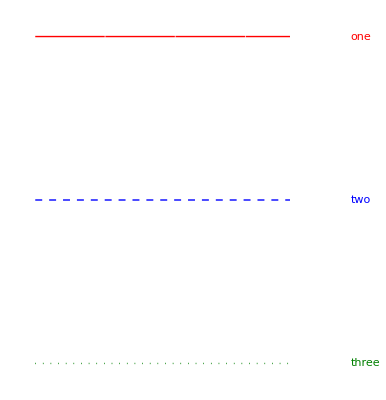

```mathematica
{{{solid,red},"one"},{{Dashed,blue},"two"},{{Dotted,green},"three"}}
makeLineLegend[%,LinelengthScale->1.3]
```

### Module makeLegend[] to Produce Plot Legend which contains user-specified symbols & text -- include via Show[..., Epilog -> Inset[makeLineLegend[...], Scaled[{0.6, 0.82}]]]

```mathematica
Options[makeLegend]=
{LinelengthScale->1(*amount to scale length of drawn line*),
SeparationScale->1(*amount to scale gap between drawn line and text*),
ParskipScale->1(*amount to scale vertical distance between text lines*)};
(**)
makeLegend[list_,opts:OptionsPattern[]]:=Module[
{lines=Dimensions[list][[1]](*# of lines*),
linelength(*length of drawn line; works for 3-5 lines*),
separation(*separation between drawn line and text; works for 3-5 lines*),
parskip(*vertical separation between two text text; works for 3-5 lines*),
linelengthscale=OptionValue[LinelengthScale],separationscale=OptionValue[SeparationScale],parskipscale=OptionValue[SeparationScale]},
linelength=(35-2.5(lines-1))*linelengthscale;
separation=(10-0.35(lines-1))*separationscale;
parskip=(30-2.5(lines-1))*parskipscale;
Show[Table[
Graphics[Flatten[{list[[i,1]],Text[list[[i,2]],{linelength+separation,(lines-1-i)parskip},{-1,0}]}]],
{i,1,lines}],
BaseStyle->{Thickness[Large],FontSize->14,FontFamily->"Times"(*,Italic*)},AspectRatio->Automatic,ImageSize->{Automatic,(lines-1)*parskip*parskipscale}]]
```

example:

{{{Dashing[{1,0}],RGBColor[0.368417, 0.506779, 0.709798],Disk[{5,40},4],AbsoluteThickness[1],Line[{{0,10},{20,10}}]},^4He HIγS data at 61MeV},{{Dashing[{1,0}],RGBColor[1, 0, 0],Line[{{30,10},{40,10}}]},^3He}}

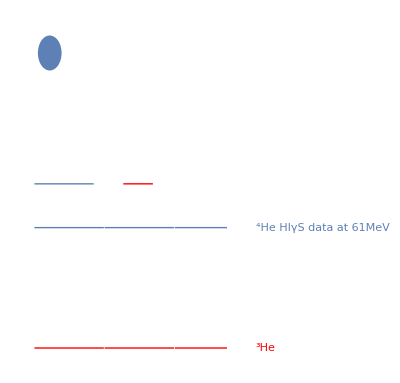

```mathematica
{{{solid,RGBColor[0.368417,0.506779,0.709798],Disk[{10/2,40},4],AbsoluteThickness[1],
Line[{{0,10},{20,10}}]},"^4He HIγS data at 61MeV"},
{{solid,red,Line[{{30,10},{40,10}}]},"^3He"}}
makeLineLegend[%,LinelengthScale->2]
```

## Module for small-sized graphics in .pdf

old file size with poor rendering was 0.25MB. With much better rendering, we now get same size (using rastered output).
option “magnification” (last argument) increases resolution quality but increases filesize -- starts to sputter when set to 4 or more.

```mathematica
rasteredexport[filename_,plotname_,resolution_(*300 is well enough for good ressolution; 450 is quite perfect*),imagesize_]:=
Export[filename,plotname,"AllowRasterization"->True,ImageSize->imagesize(*360*),ImageResolution->resolution]
```

another way was the following, but it produced garbage if figure too complicated (like clover-plot).

```mathematica
(*rasteredexport[filename_,plotname_,magnification_:3]:=
Export[filename,plotname,Rasterize[Magnify[plotname,magnification(*magnification of 3 looks fine on hgrie's terminal, with acceptable filesize*)],"Image"],ImageResolution->600(*no noticeable difference with this option*)]*)
```

## Module: figures in Column, Row or Array to have same (frame) size: alignedGraphicsColumn/Row/Array[list,opts]

hgrie July 2017
mostly from https://mathematica.stackexchange.com/questions/88312/remove-the-extra-white-space-padding-introduced-by-implicit-use-of-inset-in-grap , 
but added Row and more examples how to get good grids for Array

#### Define auxiliary functions

```mathematica
padding[g_Graphics]:=With[{im=Image[Show[g,LabelStyle->White,Background->White]]},BorderDimensions[im]]
leftRightPadding[graphicsSequence__Graphics]:={1+Max/@Transpose@(First/@#)&@(padding/@List@graphicsSequence),{Automatic,Automatic}}
maxPadding[graphicsSequence__Graphics]:=1+{Max/@Transpose@(First/@#),Max/@Transpose@(Last/@#)}&@(padding/@List@graphicsSequence)
```

### Define function to align several graphics into same sizes in a column: alignedGraphicsColumn[list,opts]

Explain Options:
 Accepts Graphics options for the whole image.

In the current implementation, ImageSize is broken, but it's functionality is mimicked with:

SubImageWidth: an option that determines the figure width.
        Choosing a positive real number x mimics the behavior of ImageSize -> x.
        Full scales all of the sub-plots so that they all have the width of the sub-plot with the largest width, and the ImageSize is then this width.
        Automatic is the default: the ImageSize is the width of the sub-plot with the largest width.

FrameAligned determines the alignment functionality.
        All: all plots get the same ImagePadding, and so the plots get lined up nicely, with lots of space between them, which can be fixed with Spacings.
        LeftOnly: all plots get the same ImagePadding on the left and the right, which aligns the left sides of the frames only, unless all sub-plots have the same ImageSize.
        None: applies no ImagePadding, so the plots do not line up.

Spacings: works as advertised in GraphicsGrid and related functions.

#### Define function alignedGraphicsColumn[list_,opts:OptionsPattern[]]

```mathematica
Clear[alignedGraphicsColumn]
(*options*)
Options[alignedGraphicsColumn]=Join[{Spacings->0,FrameAligned->LeftOnly,SubImageWidth->Automatic},Options[Graphics]];
(*error message texts*)
alignedGraphicsColumn::faligned="Value of option FrameAligned is not All, None, or LeftRight.";
alignedGraphicsColumn::width="Value of option SubImageWidth is not Full, Automatic, or a positive machine number.";
(**)
alignedGraphicsColumn[list_,opts:OptionsPattern[]]:=Module[{sizes,width,plots,optWidth=OptionValue[SubImageWidth]},Which[And[optWidth=!=Automatic,optWidth=!=Full,!NumericQ@optWidth],Return[Message[alignedGraphicsColumn::width]],optWidth===Automatic,plots=list,optWidth===Full,plots=Show[#,ImageSize->Max@First@(ImageDimensions/@list)]&/@list,NumericQ@optWidth,Which[!Element[optWidth,Reals],Return[Message[alignedGraphicsColumn::width]],optWidth≤0,Return[Message[alignedGraphicsColumn::width]],optWidth>0,plots=Show[#,ImageSize->optWidth]&/@list],True,plots=list];Which[And@@(OptionValue[FrameAligned]=!=#&/@{LeftOnly,All,None}),Return[Message[alignedGraphicsColumn::faligned]],OptionValue[FrameAligned]===LeftOnly,plots=Show[#,ImagePadding->leftRightPadding@@plots]&/@plots,OptionValue[FrameAligned]===All,plots=Show[#,ImagePadding->maxPadding@@plots]&/@plots,OptionValue[FrameAligned]===None,True];sizes=ImageDimensions/@plots;width=Max@sizes[[All,1]];sizes=sizes[[All,2]]+Join[{0},ConstantArray[OptionValue[Spacings],Length@plots-1]];Graphics[Table[Inset[plots[[i]],{0,-Plus@@sizes[[;;i]]},ImageScaled[{0,0}]],{i,Length[plots]}],ImageSize->{width,Plus@@sizes},ImagePadding->None,PlotRange->{{0,width},{-Plus@@sizes,0}},AspectRatio->Plus@@sizes/width,PlotRangePadding->None,FilterRules[{opts},Options[Graphics]]]]
```

#### Example

```mathematica
(*p1=Plot[x,{x,0,1},Frame->True,FrameLabel->{None,"left"},BaseStyle->{FontSize->10},ImageSize->300];
p2=Plot[x^2,{x,0,1},Frame->True,FrameLabel->{{None,"right"},{"bottom",None}},BaseStyle->{FontSize->10},ImageSize->255,AspectRatio->1];
p3=Plot[(x-1)^3,{x,0,1},Frame->True,FrameLabel->{"bottom",None},BaseStyle->{FontSize->10},ImageSize->255];
alignedGraphicsColumn[{p1,p2,p3},FrameAligned->All,SubImageWidth->200,Spacings->20,Background->LightBlue]
alignedGraphicsColumn[{p1,p2,p3},FrameAligned->LeftOnly,SubImageWidth->Automatic,Spacings->20]
alignedGraphicsColumn[{p1,p2,p3},FrameAligned->LeftOnly,SubImageWidth->Full]
alignedGraphicsColumn[{p1,p2,p3},FrameAligned->None]
Clear[p1,p2,p3]*)
```

### Define function to align several graphics into same HEIGHTS in a row: alignedGraphicsRow[list,opts]

```mathematica
Clear[alignedGraphicsRow]
(*options*)
Options[alignedGraphicsRow]=Join[{Spacings->0,ImageWidth->Automatic},Options[Graphics]];
(*error messge text*)
alignedGraphicsRow::width="Value of option ImageWidth is not Automatic or a positive machine number.";
(**)
alignedGraphicsRow[list_,verticalSize_:250(*need to specify vertical size; defult is 250*),opts:OptionsPattern[]]:=
Module[{p1h,p1v,p2h,p2v,verticalPadding,newlist},
newlist=Table[Show[list[[i]],ImageSize->{Automatic,verticalSize}],{i,1,Length[list]}];
Do[{ph[i],pv[i]}=padding[newlist[[i]]],{i,1,Length[newlist]}];
verticalPadding=Max/@Transpose[Table[pv[i],{i,1,Length[newlist]}]];
Row[Table[Show[newlist[[i]],ImagePadding->{ph[i],verticalPadding}],{i,1,Length[newlist]}]]]
```

#### Example: when both plots have same AspectRatio, then plot frames are actually also drawn at same size!

```mathematica
(*plot1=Plot[x^2,{x,0,1},Frame->True,FrameLabel->{"x (nm)","y (nm)"},BaseStyle->{FontFamily->"Arial",20},ImageSize->{Automatic,verticalSize}];
plot2=Plot[x^2,{x,-10,10},PlotRange->{-10,1000},Frame->True,FrameLabel->{"x^2",None},BaseStyle->{FontFamily->"Arial",20},AspectRatio->1,ImageSize->{Automatic,verticalSize}];
plot3=Plot[x^2,{x,-100,100},PlotRange->{-10,100000},Frame->True,FrameLabel->{"x^2",None},BaseStyle->{FontFamily->"Arial",20},ImageSize->{Automatic,verticalSize}];
alignedGraphicsRow[{plot1,plot2}]
alignedGraphicsRow[{plot1,plot3}]
alignedGraphicsRow[{plot1,plot2},150]
alignedGraphicsRow[{plot1,plot3},150]
Clear[plot1,plot2,plot3]*)
```

### Define function to align several graphics into same sizes in an array: alignedGraphicsGrid[list,opts]

#### Define function alignedGraphicsGrid[list,opts]

```mathematica
Clear[alignedGraphicsGrid]
(*options*)
Options[alignedGraphicsGrid]=Join[{Spacings->0,ImageWidth->Automatic},Options[Graphics]];
(*error messge text*)
alignedGraphicsGrid::width="Value of option ImageWidth is not Automatic or a positive machine number.";
(**)
alignedGraphicsGrid[list_,opts:OptionsPattern[]]:=Module[{size,sizes,width,height,plots,space=OptionValue[Spacings],optWidth=OptionValue[ImageWidth]},plots=Map[Show[#,ImagePadding->maxPadding@@Flatten@list]&,list,{2}];size=ImageDimensions@plots[[1,1]];sizes=space {Range[0,Last@#]/.{a___,b_,c_}:>{a,b,b},Range[0,First@#]}+size {Range[0,Last@#],Range[1+First@#]}&@Dimensions@plots;Which[And[optWidth=!=Automatic,!NumericQ@optWidth],Return[Message[alignedGraphicsGrid::width]],NumericQ@optWidth,plots=Map[Show[#,ImageSize->optWidth/sizes[[1,-1]] ImageDimensions[#][[1]]]&,plots,{2}];sizes=sizes*optWidth/sizes[[1,-1]],optWidth===Automatic,plots=list];height=sizes[[2,-2]];width=sizes[[1,-1]];Graphics[MapThread[Inset[#1,#2,ImageScaled[{0,0}]]&,{plots,Transpose@Outer[List,sizes[[1, ;;-2]],-sizes[[2, ;;-2]]]},2],ImageSize->{sizes[[1,-1]],height},ImagePadding->None,PlotRange->{{0,width},{-height,0}},AspectRatio->height/width,PlotRangePadding->None,FilterRules[{opts},Options[Graphics]]]]
```

#### Examples

```mathematica
(*p1=Plot[x,{x,0,1},Frame->True,FrameLabel->{None,"left"},BaseStyle->{FontSize->10},ImageSize->300];
p2=Plot[x^2,{x,0,1},Frame->True,FrameLabel->{{None,"right"},{"bottom",None}},BaseStyle->{FontSize->10},ImageSize->255,AspectRatio->1];
p3=Plot[(x-1)^3,{x,0,1},Frame->True,FrameLabel->{"bottom",None},BaseStyle->{FontSize->10},ImageSize->255];*)
```

It does NOT work out of the box:

```mathematica
(*alignedGraphicsGrid[{{p1,p2},{p3,p1},{p1,p1}}/.HoldPattern[FrameLabel->_]:>Sequence[](*eliminates all frame labels*),
Spacings->{-22,-20}(*needs fine tuning*),ImageWidth->400]*)
```

```mathematica
(*alignedGraphicsGrid[{{p1,p2},{p3,p1},{p1,p1}},Spacings->{-22,-20}(*needs fine tuning*),ImageWidth->400]*)
```

But I can fix that:

```mathematica
(*commonimagesize=200;commonaspectratio=1/GoldenRatio;
alignedGraphicsGrid[{
{Show[p1,ImageSize->commonimagesize,AspectRatio->commonaspectratio],Show[p2,ImageSize->commonimagesize,AspectRatio->commonaspectratio]},
{Show[p3,ImageSize->commonimagesize,AspectRatio->commonaspectratio],Show[p1,ImageSize->commonimagesize,AspectRatio->commonaspectratio]},
{Show[p3,ImageSize->commonimagesize,AspectRatio->commonaspectratio],Show[p1,ImageSize->commonimagesize,AspectRatio->commonaspectratio]}}(*/.HoldPattern[FrameLabel->_]:>Sequence[](*eliminates all frame labels*)*),
Spacings->{-22,-20}(*needs fine tuning*),ImageWidth->2*commonimagesize]
Clear[commonimagesize,commonaspectratio]*)
```

To eliminate frame labels, activate line “/.HoldPattern[FrameLabel→_]:>Sequence[]”:

```mathematica
(*commonimagesize=200;commonaspectratio=1/GoldenRatio;
alignedGraphicsGrid[{
{Show[p1,ImageSize->commonimagesize,AspectRatio->commonaspectratio],Show[p2,ImageSize->commonimagesize,AspectRatio->commonaspectratio]},
{Show[p3,ImageSize->commonimagesize,AspectRatio->commonaspectratio],Show[p1,ImageSize->commonimagesize,AspectRatio->commonaspectratio]},
{Show[p3,ImageSize->commonimagesize,AspectRatio->commonaspectratio],Show[p1,ImageSize->commonimagesize,AspectRatio->commonaspectratio]}}/.HoldPattern[FrameLabel->_]:>Sequence[](*eliminates all frame labels*),
Spacings->{-22,-20}(*needs fine tuning*),ImageWidth->2*commonimagesize]
Clear[commonimagesize,commonaspectratio]*)
```

and now something fancy: without any frame labels:

```mathematica
(*numberofColumns=2;imagesize=600;commonaspectratio=1/GoldenRatio;
plotlist={p1,p2,p1,p3,p3,p3};
Module[{firstinlastrow,polstableforPlot,commonimagesize=imagesize/numberofColumns},
firstinlastrow=(Dimensions[Partition[plotlist,numberofColumns]][[1]]-1)*numberofColumns+1;
polstableforPlot=Flatten[Transpose[Partition[plotlist,Dimensions[Partition[plotlist,numberofColumns]][[1]]]]];
Labeled[
alignedGraphicsGrid[Partition[
Table[Show[plotlist[[i]],
(*FrameTicks->{{All,All},{All,All}},*)
FrameTicksStyle->Which[
i==firstinlastrow,{{Automatic(*left*),Automatic(*right*)},{Automatic(*bottom*),Automatic(*top*)}},
i>firstinlastrow,{{Directive[FontOpacity->0](*left*),Automatic(*right*)},{Automatic(*bottom*),Automatic(*top*)}},
Mod[i,numberofColumns]==1,{{Automatic(*left*),Automatic(*right*)},{Directive[FontOpacity->0](*bottom*),Automatic(*top*)}},
True,{{Directive[FontOpacity->0](*left*),Automatic(*right*)},{Directive[FontOpacity->0](*bottom*),Automatic(*top*)}}],
ImageSize->commonimagesize,AspectRatio->commonaspectratio],
{i,1,Length[plotlist]}],
numberofColumns]/.
HoldPattern[FrameLabel->_]:>Sequence[](*eliminates FrameLabel from plots*),
Spacings->{-22(*horizontal*),-20(*vertical*)}(*Scaled[-0.1(*0.12*)*750/imagesize]*)(*needs fine tuning*),
ImageWidth->imagesize,Background->Transparent],
(*now the label around the grid*)
StringForm["d``/dξ [inverse canonical units]",σ],{Left},
RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18]]]
Clear[numberofColumns,imagesize,commonaspectratio,plotlist]*)
```

and now with frame labels on outer plots

```mathematica
(*numberofColumns=2;imagesize=600;commonaspectratio=1/GoldenRatio;
plotlist={p1,p2,p1,p3,p3,p3};
Module[{firstinlastrow,polstableforPlot,commonimagesize=imagesize/numberofColumns},
firstinlastrow=(Dimensions[Partition[plotlist,numberofColumns]][[1]]-1)*numberofColumns+1;
polstableforPlot=Flatten[Transpose[Partition[plotlist,Dimensions[Partition[plotlist,numberofColumns]][[1]]]]];
Labeled[
alignedGraphicsGrid[Partition[
Table[Show[plotlist[[i]],
FrameLabel->{
{(*left style*) Style["mylabel",Which[i==firstinlastrow,Black,i>firstinlastrow,Directive[FontOpacity->0],Mod[i,numberofColumns]==1,Black,True,Directive[FontOpacity->0]]],
(*right style*)None},
{(*bottom style*)Style["ω_lab [MeV]",Which[i≥firstinlastrow,Black,True,Directive[FontOpacity->0]]],
(*top style*)None}},
FrameTicksStyle->Which[
i==firstinlastrow,{{Automatic(*left*),Automatic(*right*)},{Automatic(*bottom*),Automatic(*top*)}},
i>firstinlastrow,{{Directive[FontOpacity->0](*left*),Automatic(*right*)},{Automatic(*bottom*),Automatic(*top*)}},
Mod[i,numberofColumns]==1,{{Automatic(*left*),Automatic(*right*)},{Directive[FontOpacity->0](*bottom*),Automatic(*top*)}},
True,{{Directive[FontOpacity->0](*left*),Automatic(*right*)},{Directive[FontOpacity->0](*bottom*),Automatic(*top*)}}],
ImageSize->commonimagesize,AspectRatio->commonaspectratio],
{i,1,Length[plotlist]}],
numberofColumns],
Spacings->{-22(*horizontal*),-20(*vertical*)}(*Scaled[-0.1(*0.12*)*750/imagesize]*)(*needs fine tuning*),
ImageWidth->imagesize,Background->Transparent],
(*now the label around the grid*)
StringForm["d``/dξ [inverse canonical units]",σ],{Left},
RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18]]]
Clear[numberofColumns,imagesize,commonaspectratio,plotlist]*)
```

or even tick comments also on top and right

```mathematica
(*numberofColumns=3;imagesize=900;commonaspectratio=1/GoldenRatio;
plotlist={p1,p2,p1,p3,p3,p3,p3,p3,p3};
Module[{firstinlastrow,polstableforPlot,commonimagesize=imagesize/numberofColumns,numberofRows=Length[plotlist]/numberofColumns},
firstinlastrow=(Dimensions[Partition[plotlist,numberofColumns]][[1]]-1)*numberofColumns+1;
polstableforPlot=Flatten[Transpose[Partition[plotlist,Dimensions[Partition[plotlist,numberofColumns]][[1]]]]];
Labeled[
alignedGraphicsGrid[Partition[
Table[Show[plotlist[[i]],
FrameTicks->{{All,All},{All,All}},
FrameLabel->{
{(*left style*) Style["left",Which[i==firstinlastrow,Black,i>firstinlastrow,Directive[FontOpacity->0],Mod[i,numberofColumns]==1,Black,True,Directive[FontOpacity->0]]],
(*right style*)Style[StringForm["right ``",i],Which[Mod[i,numberofColumns]==0,Black,True,Directive[FontOpacity->0]]]},
{(*bottom style*)Style["ω_lab [MeV]",Which[i≥firstinlastrow,Black,True,Directive[FontOpacity->0]]],(*top style*)None}},
FrameTicksStyle->Which[
i==1(*top left*),{{Automatic(*left*),Directive[FontOpacity->0](*right*)},{Directive[FontOpacity->0](*bottom*),Automatic(*top*)}},
i==firstinlastrow(*bottom left*),{{Automatic(*left*),Directive[FontOpacity->0](*right*)},{Automatic(*bottom*),Directive[FontOpacity->0](*top*)}},
i==numberofColumns(*top right*),{{Directive[FontOpacity->0](*left*),Automatic(*right*)},{Directive[FontOpacity->0](*bottom*),Automatic(*top*)}},
i==Length[plotlist](*bottom right*),{{Directive[FontOpacity->0](*left*),Automatic(*right*)},{Automatic(*bottom*),Directive[FontOpacity->0](*top*)}},
i<numberofColumns(*others in top row*),
{{Directive[FontOpacity->0](*left*),Directive[FontOpacity->0](*right*)},{Directive[FontOpacity->0](*bottom*),Automatic(*top*)}},
i>firstinlastrow∧i<Length[plotlist](*others in bottom row*),{{Directive[FontOpacity->0](*left*),Directive[FontOpacity->0](*right*)},{Automatic(*bottom*),Directive[FontOpacity->0](*top*)}},
Mod[i,numberofColumns]==0(*others in leftmost column*),
{{Directive[FontOpacity->0](*left*),Automatic(*right*)},{Directive[FontOpacity->0](*bottom*),Directive[FontOpacity->0](*top*)}},
Mod[i,numberofColumns]==1(*others in rightmost column*),
{{Automatic(*left*),Directive[FontOpacity->0](*right*)},{Directive[FontOpacity->0](*bottom*),Directive[FontOpacity->0](*top*)}},
True(*all else: those in middle*),{{Directive[FontOpacity->0](*left*),Directive[FontOpacity->0](*right*)},{Directive[FontOpacity->0](*bottom*),Directive[FontOpacity->0](*top*)}}],
ImageSize->commonimagesize,AspectRatio->commonaspectratio],
{i,1,Length[plotlist]}],
numberofColumns],
Spacings->{-70(*horizontal*),-40(*vertical*)}(*Scaled[-0.1(*0.12*)*750/imagesize]*)(*needs fine tuning*),
ImageWidth->imagesize,Background->Transparent],
(*now the label around the grid*)
StringForm["d``/dξ [inverse canonical units]",σ],{Left},
RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18]]]
Clear[numberofColumns,imagesize,commonaspectratio,plotlist]*)
```

```mathematica
Clear[p1,p2,p3]
```

#### OLD, DOES NOT WORK

Definitions needed for the module:

```mathematica
(*getPadding[g_]:=Module[{im},im=Image[Show[g,LabelStyle->White,Background->White]];BorderDimensions[im]]
paddings[plots_]:=Table[getPadding[plots[[i,j]]],{i,1,Dimensions[plots][[1]]},{j,1,Dimensions[plots][[2]]}]
findMaxVerticalPadding[paddingtable_]:=Max/@Transpose[Flatten[Table[paddingtable[[i,j,2]],{i,1,Dimensions[paddingtable][[1]]},{j,1,Dimensions[paddingtable][[2]]}],1]]
findMaxHorizontalPadding[paddingtable_]:=Max/@Transpose[Flatten[Table[paddingtable[[i,j,1]],{i,1,Dimensions[paddingtable][[1]]},{j,1,Dimensions[paddingtable][[2]]}],1]]*)
```

problem: using Spacing in GraphicsGrid also changes size of individual figures, so need ImageSize to re-adjust

“plottable” argument must be a MATRIX OF PLOTS!!

options are arguments passed to GraphicsGrid -- default: Automatic

```mathematica
(*makeGridPlot[plottable_(*matrix of plots*),opts:OptionsPattern[]]:=Module[{paddinglist=paddings[plottable],newVerticalPadding,newHorizontalPadding},
newVerticalPadding=findMaxVerticalPadding[paddinglist];newHorizontalPadding=findMaxHorizontalPadding[paddinglist];GraphicsGrid[Table[Show[plottable[[i,j]],
ImagePadding->{newHorizontalPadding(*paddinglist[[i,j,1]]*),newVerticalPadding(*paddinglist[[i,j,2]]*)}],
{i,1,Dimensions[paddinglist][[1]]},{j,1,Dimensions[paddinglist][[2]]}],
opts]]*)
```

Example:

makeGridPlot[plottablex]
makeGridPlot[plottablex, 
Spacings->{-2, -15} (*{-2,-40}*)(*no x-axis label, but numbers*) (*{-2,-55}*)(*no x-axis label or numbers*)(*Spacing; can be "Automatic"*), 
ImageSize-> 2*(ImageSize /. plotoptions)[[1]] + 30(*ImageSize*)]

### Module: plotGrid is better than the above makeGridPlot[] for alignedGraphicsColumn/Row/Array

https://mathematica.stackexchange.com/questions/6877/do-i-have-to-code-each-case-of-this-grid-full-of-plots-separately/6882#6882

“The Inset takes care of the relative sizing and the correct placement of the individual plots. To do this most easily, I set the PlotRange of the enclosing Graphics in which the Insets live to {w, h}, identical to the desired ImageSize of the result. “

```mathematica
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

## Module: myYAxesWithDifferentScalesPlot[] : plot whose y axes are scaled by different amounts

```mathematica
Options[myYAxesWithDifferentScalesPlot]={ShowSecondPlot->False(*if True, show second plot*),
TopTicks->Automatic,BottomTicks->Automatic,(*can specify Top & Bottom Ticks for θ plots*)
"PlotOptions"->{}}
myYAxesWithDifferentScalesPlot[function_,scale_,{x_,xmin_,xmax_},opts:OptionsPattern[{Plot,myYAxesWithDifferentScalesPlot}]]:=
Module[{fgraph,ggraph,frange,grange,fticks,gticks},
fgraph=Plot[function,{x,xmin,xmax},Axes->True,Frame->True,Evaluate[FilterRules[{opts},Options[Plot]]]];fticks=Charting`FindTicks[{0,1},{0,1}]@@PlotRange[fgraph][[2]];
ggraph=Plot[scale*function,{x,xmin,xmax},Axes->True,
ScalingFunctions->{Identity,If[Sign[scale]==-1,"Reverse",Identity]},
PlotStyle->If[OptionValue["ShowSecondPlot"],{{Dotted,Red}},Transparent]];
{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};
gticks=MapAt[#*Sign[scale]&,MapAt[#*Sign[scale]/scale&,fticks,{All,1}],{All,2}]/.{-""->""};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->True(*was "False, but with True, coordinate axes are displayed as well*),Frame->True,FrameTicks->{{All,gticks},{OptionValue[BottomTicks],OptionValue[TopTicks]}}]]
```

{ShowSecondPlot→False,TopTicks→Automatic,BottomTicks→Automatic,PlotOptions→{}}

#### Following Takes Care of Bug for FrameTicks style: not all ticks are made black and thicker

https://mathematica.stackexchange.com/questions/155276/how-do-i-adjust-the-thickness-of-all-the-frameticks

```mathematica
Initial/:Verbatim[TagSetDelayed][Initial[sym_],lhs_,rhs_]:=With[{new=Block[{sym},TagSetDelayed[sym,lhs,rhs];
First@Language`ExtendedDefinition[sym]],protect=Unprotect[sym]},sym;
Quiet@MakeBoxes[sym[],TraditionalForm];
Unprotect[sym];
Replace[new,Rule[values_,n:Except[{}]]:>(values[sym]=DeleteDuplicates@Join[n,values[sym]]),{2}];
Protect@protect;]
```

```mathematica
Initial[Charting`ScaledTicks]/:Charting`ScaledTicks[a__][b___]/;!TrueQ@$Fix:=Block[{$Fix=True},Charting`ScaledTicks[a][b]/.AbsoluteThickness[.1]->Sequence[]]
```

## Module to Save and Read .m files. Directory path and file name set here

#### Need a Date

```mathematica
date:=
ToString[
StringForm["``````````",
				NumberForm[Date[][[1]]],
				If[ToExpression[ToString[NumberForm[Date[][[2]]]]]<10,0,1],
				If[ToExpression[ToString[NumberForm[Date[][[2]]]]]≥10,
					ToExpression[ToString[NumberForm[Date[][[2]]]]]-10,
					ToExpression[ToString[NumberForm[Date[][[2]]]]]],
				If[ToExpression[ToString[NumberForm[Date[][[3]]]]]<10,0,
					If[ToExpression[ToString[NumberForm[Date[][[3]]]]]<20,1,
					If[ToExpression[ToString[NumberForm[Date[][[3]]]]]<30,2,3]]],
				Mod[ToExpression[ToString[NumberForm[Date[][[3]]]]],10],
]
]
```

#### Function to save the mathematica "executables" into files, and read it in again

Not the executables .mx are saved because of compatibility issues, but the .m files of a session, i.e. all definitions and numerical values which have been made/derived up to that point in a session.

Example filename: 	<directory>/<name>.<comment>.<versionnumber>.<date>.save<savenumber>, where the last number is the save number.
		 	mxfiles/partialwaveprojectors.noDwaves.v1.0.20100626.save1

```mathematica
mysave[mxdirectory0_,name_,comment_,fileversion0_,date0_,number_]:=
Module[{filename=
ToString[
StringForm["``/``.``.``.``.save``",
mxdirectory0,name,comment,fileversion0,date0,number]]},
Print[StringForm["CPU time used so far: `` seconds",Round[TimeUsed[]]]];
Print[StringForm["Memory currently used: `` bytes",MemoryInUse[]]];
Print[StringForm["Memory freed by invoking Share[]: `` bytes",Share[]]];
Print[StringForm["Save filename: ``",filename]];
(*Print[StringForm["DumpSave filename: ``",filename]];*)
If[FileNames[filename]≠{},DeleteFile[filename]]; (*just to make sure the file does not exist -- if it would, math..ematica would _append_ to that file!*)
Save[filename,"`*"]
]
```

```mathematica
myget[mxdirectory0_,name_,comment_,fileversion0_,date0_,number_]:=
Module[{filename=
ToString[
StringForm["``/``.``.``.``.save``",
mxdirectory0,name,comment,fileversion0,date0,number]]},
Print[StringForm["Get file: ``",filename]];
Get[filename];
]
```

#### Directories, file names

Directory for mx-executable files: <startdirectory>/mxfiles

```mathematica
mxdir="mxfiles";
```

```mathematica
firstname="";
```

## Module to free memory

```mathematica
freeMemory:=Module[{},
Print[StringForm["CPU time used so far:              `` seconds",NumberForm[Round[TimeUsed[]],DigitBlock->3,NumberSeparator->" "]]];
Print[StringForm["Memory currently used:             `` bytes",NumberForm[MemoryInUse[],12,NumberPadding->{" ",""},DigitBlock->3,NumberSeparator->" "]]];
Print[StringForm["Memory freed by invoking Share[]:  `` bytes",NumberForm[Share[],12,NumberPadding->{" ",""},DigitBlock->3,NumberSeparator->" "]]];
Print[StringForm["Memory still used:                 `` bytes",NumberForm[MemoryInUse[],12,NumberPadding->{" ",""},DigitBlock->3,NumberSeparator->" "]]]]
```

## Module myrounding[number,{digits before decimal point,digits after decimal point}]: numbers in fixed format with signs up front, padding (“ “ before, “0” after decimal dot), Scientific Notation if outside range,etc --- Good for Tables!!!

```mathematica
myrounding[number_,{beforedot_Integer,afterdot_Integer}]:=NumberForm[number,{beforedot+afterdot,afterdot},NumberSigns->{"-","+"},SignPadding->True,NumberPadding->{" ","0"},DigitBlock->3,NumberSeparator->" ",ScientificNotationThreshold->{-afterdot,beforedot}]
```

```mathematica
myrounding[5555.55555555 10^10,{3,3}]
myrounding[5555.55555555,{3,3}]
myrounding[555.55555555,{3,3}]
myrounding[55.55555555,{3,3}]
myrounding[0.00555555,{3,3}]
myrounding[0.000055555,{3,3}]
```

+  5.556×10^13

+  5.556×10^3

+555.556

+ 55.556

+  0.006

+  5.556×10^-5

## 1. Preparations

### Momenta, Momentum Combinations and Polarisations SPECIFIC TO ONEBODY

#### Photon momenta and polarisation vectors

Rotation matrix FROM incoming TO outgoing photon momentu: θ is the scattering angle

```mathematica
MatrixForm[R={{Cos[θ],0,Sin[θ]},{0,1,0},{-Sin[θ],0,Cos[θ]}}]
```

(Cos[θ] | 0 | Sin[θ]
0 | 1 | 0
-Sin[θ] | 0 | Cos[θ])

```mathematica
kvec={0,0,ω};
kvecp=ω{Sin[θ],0,Cos[θ]};(* identical to R.kvec *)
R.kvec-%
```

{0,0,0}

unit vectors

```mathematica
khatvec=kvec/ω;
khatvecp=kvecp/ω;(* identical to R.khatvec *)
R.khatvec-%
```

{0,0,0}

unit vectors:
kartesisch:

```mathematica
evec[x]={1,0,0};
evec[y]={0,1,0};
evec[z]={0,0,1};
```

Cartesian polarisation vectors of the incoming photon:

```mathematica
ϵvec[x]=evec[x];
ϵvec[y]=evec[y];
```

spherical polarisation vectors of the incoming photon:

```mathematica
ϵvec[1]=-1/Sqrt[2](evec[x]+I evec[y]);
(*ϵ[0]=ez;*)
ϵvec[-1]=1/Sqrt[2](evec[x]-I evec[y]);
```

spherical polarisation vectors of the outgoing photon:

```mathematica
ϵvecp[1]={-Cos[θ]/(√2),-ⅈ/(√2),Sin[θ]/(√2)};(* identical to R.ϵvec[1]*)
(R.ϵvec[1]-%)//FullSimplify
ϵvecp[-1]={Cos[θ]/(√2),-ⅈ/(√2),-Sin[θ]/(√2)};(* identical to R.ϵvec[-1]*)
(R.ϵvec[-1]-%)//FullSimplify
```

{0,0,0}

{0,0,0}

spherical polarisation vectors of the outgoing photon conjugated (con, das ist eigentlich die relevante Darstellung):

```mathematica
ϵvecpdag[1]={-Cos[θ]/(√2),ⅈ/(√2),Sin[θ]/(√2)};
ϵvecpdag[-1]={Cos[θ]/(√2),ⅈ/(√2),-Sin[θ]/(√2)};
```

Make sure the circpol photon helicities of the out state are ALWAYS daggered by un-defining their undaggered form

```mathematica
Clear[ϵvecp]
```

Cartesian polarisation vectors of the outgoing photon:

```mathematica
ϵvecp[x]={Cos[θ],0,-Sin[θ]};(* identical to R.ϵvec[x]*)
(R.ϵvec[x]-%)//FullSimplify
ϵvecp[y]=evec[y];(* identical to R.ϵvec[y]*)
(R.ϵvec[y]-%)//FullSimplify
```

{0,0,0}

{0,0,0}

NO complex conjugation necessary for Cartesian vectors, but defining them here makes lif easier later

```mathematica
ϵvecpdag[x]=ϵvecp[x];
ϵvecpdag[y]=ϵvecp[y];
```

#### Vector of the Integration Variable p

```mathematica
pvec=p{Sin[θp] Cos[ϕp],Sin[θp] Sin[ϕp],Cos[θp]};
```

#### Vector of the Auxiliary Variable pp(rime)=p+(k-kprime)/2

```mathematica
pvecp=pvec+(kvec-kvecp)/2;
```

```mathematica
psquarep=Simplify[pvecp.pvecp,{ω>0,θ>0,p>0,θp>0,ϕp>0}];
pp=Simplify[psquarep^(1/2),{ω>0,θ>0,p>0,θp>0,ϕp>0}]
```

√(p^2+ω^2/2+p ω Cos[θp]-1/2 ω Cos[θ] (ω+2 p Cos[θp])-p ω Cos[ϕp] Sin[θ] Sin[θp])

```mathematica
θpp=Simplify[ArcCos[pvecp[[3]]/pp],{ω>0,θ>0,p>0,θp>0,ϕp>0}]
```

ArcCos[(ω-ω Cos[θ]+2 p Cos[θp])/(√2 √(2 p^2+ω^2+2 p ω Cos[θp]-ω Cos[θ] (ω+2 p Cos[θp])-2 p ω Cos[ϕp] Sin[θ] Sin[θp]))]

```mathematica
ϕpp=Simplify[ArcTan[pvecp[[1]],pvecp[[2]]],{ω>0,θ>0,p>0,θp>0,ϕp>0}]
```

ArcTan[-ω Sin[θ]+2 p Cos[ϕp] Sin[θp],2 p Sin[θp] Sin[ϕp]]

#### Auxiliary Vectors [Beane (XXX)] and fortran README

```mathematica
qvec=pvec-pvecp+(kvecp+kvec)/2;
qvecp=pvec-pvecp+(kvecp-kvec)/2;
qvecpp=pvec-pvecp-(kvecp-kvec)/2;
```

some squares

```mathematica
qsquare=Simplify[qvec.qvec];
qsquarep=Simplify[qvecp.qvecp];
qsquarepp=Simplify[qvecpp.qvecpp];
pkdiff=Simplify[pvecp.kvecp-pvec.kvec];
```

#### Pauli Matrices

```mathematica
σ[k_]=PauliMatrix[k];
```

## 2. Calculate for Integrand with Given 1N Amplitudes A1-A6

## Prepare Integrand

### Spin Structure Terms of onebody diagrams: calculatehold: this variable called “hold” in code -- my name more imaginative

Hermitean in exchanging in vs out:  		K[(i1p,i2p),(i1,i2)] =K[(i1,i2),(i1p,i2p)]^*

#### Module for individual γN amplitudes

```mathematica
spinstructure[{i1p_,i1_}(*individual nucleon spin combination*),
{ϵvec1_(*in*),ϵvec2_(*out*)}(*polarisation vectors contracted with σ[i]*),
{kvec1_(*in*),kvec2_(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{A1_,A2_,A3_,A4_,A5_,A6_}(*fundamental 1N amplitudes*)]:=
(σ[0]*((ϵvec2.ϵvec1)*A1+
(ϵvec2.kvec1)(ϵvec1.kvec2)*A2)+
I Sum[σ[k]*((ϵvec2×ϵvec1)[[k]]),{k,1,3}]*A3+
I Sum[σ[k]*((kvec2×kvec1)[[k]]),{k,1,3}]*(ϵvec2.ϵvec1)*A4+
I Sum[σ[k]*((ϵvec1.kvec2)((ϵvec2×kvec1)[[k]])-(ϵvec2.kvec1)((ϵvec1×kvec2)[[k]])),{k,1,3}]*A5+
I Sum[σ[k]*((ϵvec1.kvec2)((ϵvec2×kvec2)[[k]])-(ϵvec2.kvec1)((ϵvec1×kvec1)[[k]])),{k,1,3}]*A6)[[i1p,i1]]
```

#### Module to make spin structures -- returns spinology[name,{Mf,Mi,λf,λi}]

evaluate with “symbolic” wfs u and w which have to be replaced by wavefuu and wavefuw below, 
and with “symbolic” 1N amplitudes A1 to A6 which have to be replaced by functions below.

```mathematica
makespinology[name_,polvecs_,kvecs_]:=
Do[
Mf=helicities[[i,1]];
Mi=helicities[[i,2]];
λf=helicities[[i,3]];
λi=helicities[[i,4]];
Print[{StringForm["Mf=``",Mf],StringForm["Mi=``",Mi],StringForm["λf=``",λf],StringForm["λi=``",λi]}];
Print[
spinology[name,{Mf,Mi,λf,λi}]=
Sum[
Sum[
Sum[
Simplify[
wavefndag[Mf,m1p,m2(*second N unchanged!*),u[holdpp],w[holdpp],holdθpp,holdϕpp(*pp=p+(kp-k)/2 above!*)](*out wf*)*
(spinstructure[{3/2-m1p,3/2-m1}(*individual nucleon spin combination*),
polvecs(*polarisation vectors contracted with σ[i]*),
kvecs(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{A1,A2,A3,A4,A5,A6}(*fundamental 1N amplitudes*)])*
wavefn[Mi,m1,m2(*second N unchanged!*),u[p],w[p],θp,ϕp](*in wf*),
{ω>0,θ>0,u>0,w>0,p>0,θp>0,ϕp>0,holdpp>0,holdθpp>0,holdϕpp>0}],
{m1,-1/2,1/2}],
{m1p,-1/2,1/2}],
{m2,-1/2,1/2}]//N
];
Clear[Mf,Mi,λf,λi],
{i,1,Dimensions[helicities][[1]]}]
```

## Different photon helicities, as prescribed by code: XY first index (X): in-γ-hel. ω=120MeV, OQ3,θ=53Degree

#### Proton (Mt3=1)

```mathematica
Aitable={-9.2201871977828979*10^(0-005),1.7146813331796387*10^(0-005),1.6203509608507570*10^(0-003),-6.0793673892958950*10^(0-004),4.9848349565209823*10^(0-004),-8.0890563516242329*10^(0-005)}
```

{-0.0000922019,0.0000171468,0.00162035,-0.000607937,0.000498483,-0.0000808906}

```mathematica
{{"(Mp,M)=11","(Mp,M)=12"},{"(Mp,M)=21","(Mp,M)=22"}}
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->53 Degree,ω->120},{i,1,2},{j,1,2}]
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

{{(Mp,M)=11,(Mp,M)=12},{(Mp,M)=21,(Mp,M)=22}}

{{-0.000066425+0. ⅈ,-0.00135185+0. ⅈ},{0.00135185+0. ⅈ,-0.000066425+0. ⅈ}}

(Mp,M)=11 | -0.000066425+0. ⅈ
(Mp,M)=12 | -0.00135185+0. ⅈ
(Mp,M)=21 | 0.00135185+0. ⅈ
(Mp,M)=22 | -0.000066425+0. ⅈ

```mathematica
{{"(Mp,M)=11","(Mp,M)=12"},{"(Mp,M)=21","(Mp,M)=22"}}
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->53 Degree,ω->120},{i,1,2},{j,1,2}]
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

{{(Mp,M)=11,(Mp,M)=12},{(Mp,M)=21,(Mp,M)=22}}

{{0.+0.000657209 ⅈ,0.+0.00146905 ⅈ},{0.+0.00146905 ⅈ,0.-0.000657209 ⅈ}}

(Mp,M)=11 | 0.+0.000657209 ⅈ
(Mp,M)=12 | 0.+0.00146905 ⅈ
(Mp,M)=21 | 0.+0.00146905 ⅈ
(Mp,M)=22 | 0.-0.000657209 ⅈ

```mathematica
{{"(Mp,M)=11","(Mp,M)=12"},{"(Mp,M)=21","(Mp,M)=22"}}
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->53 Degree,ω->120},{i,1,2},{j,1,2}]
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

{{(Mp,M)=11,(Mp,M)=12},{(Mp,M)=21,(Mp,M)=22}}

{{0.-0.00156876 ⅈ,0.+0.000359228 ⅈ},{0.+0.000359228 ⅈ,0.+0.00156876 ⅈ}}

(Mp,M)=11 | 0.-0.00156876 ⅈ
(Mp,M)=12 | 0.+0.000359228 ⅈ
(Mp,M)=21 | 0.+0.000359228 ⅈ
(Mp,M)=22 | 0.+0.00156876 ⅈ

```mathematica
{{"(Mp,M)=11","(Mp,M)=12"},{"(Mp,M)=21","(Mp,M)=22"}}
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->53 Degree,ω->120},{i,1,2},{j,1,2}]
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

{{(Mp,M)=11,(Mp,M)=12},{(Mp,M)=21,(Mp,M)=22}}

{{-0.0000922019+0. ⅈ,0.00048552+0. ⅈ},{-0.00048552+0. ⅈ,-0.0000922019+0. ⅈ}}

(Mp,M)=11 | -0.0000922019+0. ⅈ
(Mp,M)=12 | 0.00048552+0. ⅈ
(Mp,M)=21 | -0.00048552+0. ⅈ
(Mp,M)=22 | -0.0000922019+0. ⅈ

#### Neutron (Mt3=2)

```mathematica
Aitable={9.7355534852733988*10^(0-004),-2.8286724790559747*10^(0-005),1.6519941597834343*10^(0-003),-3.2570723809886729*10^(0-004),4.3516048137635840*10^(0-004),-1.0945324327749114*10^(0-004)}
```

{0.000973555,-0.0000282867,0.00165199,-0.000325707,0.00043516,-0.000109453}

```mathematica
{{"(Mp,M)=11","(Mp,M)=12"},{"(Mp,M)=21","(Mp,M)=22"}}
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->53 Degree,ω->120},{i,1,2},{j,1,2}]
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

{{(Mp,M)=11,(Mp,M)=12},{(Mp,M)=21,(Mp,M)=22}}

{{0.000603942+0. ⅈ,-0.00140627+0. ⅈ},{0.00140627+0. ⅈ,0.000603942+0. ⅈ}}

(Mp,M)=11 | 0.000603942+0. ⅈ
(Mp,M)=12 | -0.00140627+0. ⅈ
(Mp,M)=21 | 0.00140627+0. ⅈ
(Mp,M)=22 | 0.000603942+0. ⅈ

```mathematica
{{"(Mp,M)=11","(Mp,M)=12"},{"(Mp,M)=21","(Mp,M)=22"}}
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->53 Degree,ω->120},{i,1,2},{j,1,2}]
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

{{(Mp,M)=11,(Mp,M)=12},{(Mp,M)=21,(Mp,M)=22}}

{{0.+0.000716641 ⅈ,0.+0.00144108 ⅈ},{0.+0.00144108 ⅈ,0.-0.000716641 ⅈ}}

(Mp,M)=11 | 0.+0.000716641 ⅈ
(Mp,M)=12 | 0.+0.00144108 ⅈ
(Mp,M)=21 | 0.+0.00144108 ⅈ
(Mp,M)=22 | 0.-0.000716641 ⅈ

```mathematica
{{"(Mp,M)=11","(Mp,M)=12"},{"(Mp,M)=21","(Mp,M)=22"}}
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->53 Degree,ω->120},{i,1,2},{j,1,2}]
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

{{(Mp,M)=11,(Mp,M)=12},{(Mp,M)=21,(Mp,M)=22}}

{{0.-0.00158218 ⅈ,0.+0.000294928 ⅈ},{0.+0.000294928 ⅈ,0.+0.00158218 ⅈ}}

(Mp,M)=11 | 0.-0.00158218 ⅈ
(Mp,M)=12 | 0.+0.000294928 ⅈ
(Mp,M)=21 | 0.+0.000294928 ⅈ
(Mp,M)=22 | 0.+0.00158218 ⅈ

```mathematica
{{"(Mp,M)=11","(Mp,M)=12"},{"(Mp,M)=21","(Mp,M)=22"}}
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->53 Degree,ω->120},{i,1,2},{j,1,2}]
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

{{(Mp,M)=11,(Mp,M)=12},{(Mp,M)=21,(Mp,M)=22}}

{{0.000973555+0. ⅈ,0.000260121+0. ⅈ},{-0.000260121+0. ⅈ,0.000973555+0. ⅈ}}

(Mp,M)=11 | 0.000973555+0. ⅈ
(Mp,M)=12 | 0.000260121+0. ⅈ
(Mp,M)=21 | -0.000260121+0. ⅈ
(Mp,M)=22 | 0.000973555+0. ⅈ

## Different photon helicities, as prescribed by code: XY first index (X): in-γ-hel. ω=105MeV, OQ0 with modifiers,θ=57Degree

#### Proton (Mt3=1): only A4≠0, set to Thomson

```mathematica
Aitable={0.0000000000000000*10^(0),0.0000000000000000*10^(0),0.0000000000000000*10^(0),-1.0657572205051689*10^(0-003),0.0000000000000000*10^(0),0.0000000000000000*10^(0)}
```

{0.,0.,0.,-0.00106576,0.,0.}

```mathematica
{{"(Mp,M)=11","(Mp,M)=12"},{"(Mp,M)=21","(Mp,M)=22"}}
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->57 Degree},{i,1,2},{j,1,2}]
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

{{(Mp,M)=11,(Mp,M)=12},{(Mp,M)=21,(Mp,M)=22}}

{{0.+0. ⅈ,0.000486809+0. ⅈ},{-0.000486809+0. ⅈ,0.+0. ⅈ}}

(Mp,M)=11 | 0.+0. ⅈ
(Mp,M)=12 | 0.000486809+0. ⅈ
(Mp,M)=21 | -0.000486809+0. ⅈ
(Mp,M)=22 | 0.+0. ⅈ

```mathematica
{{"(Mp,M)=11","(Mp,M)=12"},{"(Mp,M)=21","(Mp,M)=22"}}
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->57 Degree},{i,1,2},{j,1,2}]
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

{{(Mp,M)=11,(Mp,M)=12},{(Mp,M)=21,(Mp,M)=22}}

{{0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}}

(Mp,M)=11 | 0.+0. ⅈ
(Mp,M)=12 | 0.+0. ⅈ
(Mp,M)=21 | 0.+0. ⅈ
(Mp,M)=22 | 0.+0. ⅈ

```mathematica
{{"(Mp,M)=11","(Mp,M)=12"},{"(Mp,M)=21","(Mp,M)=22"}}
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->57 Degree},{i,1,2},{j,1,2}]
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

{{(Mp,M)=11,(Mp,M)=12},{(Mp,M)=21,(Mp,M)=22}}

{{0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}}

(Mp,M)=11 | 0.+0. ⅈ
(Mp,M)=12 | 0.+0. ⅈ
(Mp,M)=21 | 0.+0. ⅈ
(Mp,M)=22 | 0.+0. ⅈ

```mathematica
{{"(Mp,M)=11","(Mp,M)=12"},{"(Mp,M)=21","(Mp,M)=22"}}
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->57 Degree},{i,1,2},{j,1,2}]
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

{{(Mp,M)=11,(Mp,M)=12},{(Mp,M)=21,(Mp,M)=22}}

{{0.+0. ⅈ,0.000893819+0. ⅈ},{-0.000893819+0. ⅈ,0.+0. ⅈ}}

(Mp,M)=11 | 0.+0. ⅈ
(Mp,M)=12 | 0.000893819+0. ⅈ
(Mp,M)=21 | -0.000893819+0. ⅈ
(Mp,M)=22 | 0.+0. ⅈ

## Different photon helicities, as prescribed by code: XY first index (X): in-γ-hel. ω=120MeV, OQ3,θ=30Degree: here ordering of output as in trafo subroutine, i.e. first j then i in Table[]

#### Proton (Mt3=1)

```mathematica
Aitable={-1.6534407835395196*10^(0-004),1.7146813331796387*10^(0-005),1.5074446287936460*10^(0-003),-6.0793673892958950*10^(0-004),4.6071329304720160*10^(0-004),-4.3120360911345691*10^(0-005)}
```

{-0.000165344,0.0000171468,0.00150744,-0.000607937,0.000460713,-0.0000431204}

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->30 Degree,ω->120},{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | -0.000147479+0. ⅈ
(Mp,M)=21 | 0.000846347+0. ⅈ
(Mp,M)=12 | -0.000846347+0. ⅈ
(Mp,M)=22 | -0.000147479+0. ⅈ

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->30 Degree,ω->120},{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0.+0.00119031 ⅈ
(Mp,M)=21 | 0.+0.000931657 ⅈ
(Mp,M)=12 | 0.+0.000931657 ⅈ
(Mp,M)=22 | 0.-0.00119031 ⅈ

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->30 Degree,ω->120},{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0.-0.00149666 ⅈ
(Mp,M)=21 | 0.+0.000211685 ⅈ
(Mp,M)=12 | 0.+0.000211685 ⅈ
(Mp,M)=22 | 0.+0.00149666 ⅈ

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->30 Degree,ω->120},{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | -0.000165344+0. ⅈ
(Mp,M)=21 | -0.000303968+0. ⅈ
(Mp,M)=12 | 0.000303968+0. ⅈ
(Mp,M)=22 | -0.000165344+0. ⅈ

#### Neutron (Mt3=2)

```mathematica
Aitable={9.0041314215121688*10^(0-004),-2.8286724790559747*10^(0-005),1.5182220489028662*10^(0-003),-3.2570723809886729*10^(0-004),4.7293068398125503*10^(0-004),-1.4722344588238777*10^(0-004)}
```

{0.000900413,-0.0000282867,0.00151822,-0.000325707,0.000472931,-0.000147223}

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->30 Degree,ω->120},{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0.000786852+0. ⅈ
(Mp,M)=21 | 0.000880422+0. ⅈ
(Mp,M)=12 | -0.000880422+0. ⅈ
(Mp,M)=22 | 0.000786852+0. ⅈ

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->30 Degree,ω->120},{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0.+0.00119659 ⅈ
(Mp,M)=21 | 0.+0.000890284 ⅈ
(Mp,M)=12 | 0.+0.000890284 ⅈ
(Mp,M)=22 | 0.-0.00119659 ⅈ

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->30 Degree,ω->120},{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0.-0.00148142 ⅈ
(Mp,M)=21 | 0.+0.000172716 ⅈ
(Mp,M)=12 | 0.+0.000172716 ⅈ
(Mp,M)=22 | 0.+0.00148142 ⅈ

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
Aitable(*fundamental 1N amplitudes*)]/.{θ->30 Degree,ω->120},{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0.000900413+0. ⅈ
(Mp,M)=21 | -0.000162854+0. ⅈ
(Mp,M)=12 | 0.000162854+0. ⅈ
(Mp,M)=22 | 0.000900413+0. ⅈ

## Isolating different (Mp,M) contributions in Cartesian helicity-basis

### XX (first=in-photon helicity)

#### A1&A2 only probe Mp=M

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{A1(*A1*),A2(*A2*),0(*A3*),0(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | A1 Cos[θ]-A2 Sin[θ]^2
(Mp,M)=21 | 0
(Mp,M)=12 | 0
(Mp,M)=22 | A1 Cos[θ]-A2 Sin[θ]^2

#### A3 only probes Mp≠M

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),A3(*A3*),0(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0
(Mp,M)=21 | A3 Sin[θ]
(Mp,M)=12 | -A3 Sin[θ]
(Mp,M)=22 | 0

#### A4 only probes Mp≠M, and basically same as A3 (just multiplied with Cos[θ])

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),A4(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0
(Mp,M)=21 | A4 Cos[θ] Sin[θ]
(Mp,M)=12 | -A4 Cos[θ] Sin[θ]
(Mp,M)=22 | 0

#### A5 only probes Mp≠M, and basically same as A3 (just multiplied with 2 Cos[θ])

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),0(*A4*),A5(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0
(Mp,M)=21 | 2 A5 Cos[θ] Sin[θ]
(Mp,M)=12 | -2 A5 Cos[θ] Sin[θ]
(Mp,M)=22 | 0

#### A6 only probes Mp≠M, and basically same as A3 (just multiplied with 2)

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),0(*A4*),0(*A5*),A6(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}]//FullSimplify;
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0
(Mp,M)=21 | 2 A6 Sin[θ]
(Mp,M)=12 | -2 A6 Sin[θ]
(Mp,M)=22 | 0

### YX (first=in-photon helicity)

#### A1&A2 ZERO (trivial)

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{A1(*A1*),A2(*A2*),0(*A3*),0(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0
(Mp,M)=21 | 0
(Mp,M)=12 | 0
(Mp,M)=22 | 0

#### A3 probes all MEs, no imag unit

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),A3(*A3*),0(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | ⅈ A3 Cos[θ]
(Mp,M)=21 | ⅈ A3 Sin[θ]
(Mp,M)=12 | ⅈ A3 Sin[θ]
(Mp,M)=22 | -ⅈ A3 Cos[θ]

#### A4 zero

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),A4(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0
(Mp,M)=21 | 0
(Mp,M)=12 | 0
(Mp,M)=22 | 0

#### A5 probes all MEs, different lincomb than A3, imag unit

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),0(*A4*),A5(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | -ⅈ A5 Sin[θ]^2
(Mp,M)=21 | ⅈ A5 Cos[θ] Sin[θ]
(Mp,M)=12 | ⅈ A5 Cos[θ] Sin[θ]
(Mp,M)=22 | ⅈ A5 Sin[θ]^2

#### A6 only probes Mp≠M

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[x](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),0(*A4*),0(*A5*),A6(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}]//FullSimplify;
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0
(Mp,M)=21 | ⅈ A6 Sin[θ]
(Mp,M)=12 | ⅈ A6 Sin[θ]
(Mp,M)=22 | 0

### XY (first=in-photon helicity)

#### A1&A2 zero (trivial)

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{A1(*A1*),A2(*A2*),0(*A3*),0(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0
(Mp,M)=21 | 0
(Mp,M)=12 | 0
(Mp,M)=22 | 0

#### A3 only probes Mp=M!

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),A3(*A3*),0(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | -ⅈ A3
(Mp,M)=21 | 0
(Mp,M)=12 | 0
(Mp,M)=22 | ⅈ A3

#### A4 zero

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),A4(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0
(Mp,M)=21 | 0
(Mp,M)=12 | 0
(Mp,M)=22 | 0

#### A5 only probes Mp≠M, imag unit

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),0(*A4*),A5(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0
(Mp,M)=21 | ⅈ A5 Sin[θ]
(Mp,M)=12 | ⅈ A5 Sin[θ]
(Mp,M)=22 | 0

#### A6 only probes Mp≠M, no imag unit, different lincomb than A5

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[x](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),0(*A4*),0(*A5*),A6(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}]//FullSimplify;
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0
(Mp,M)=21 | 2 A6 Sin[θ]
(Mp,M)=12 | -2 A6 Sin[θ]
(Mp,M)=22 | 0

### YY (first=in-photon helicity)

#### A1 only probes Mp=M, A2 zero

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{A1(*A1*),A2(*A2*),0(*A3*),0(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | A1
(Mp,M)=21 | 0
(Mp,M)=12 | 0
(Mp,M)=22 | A1

#### A3 zero

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),A3(*A3*),0(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0
(Mp,M)=21 | 0
(Mp,M)=12 | 0
(Mp,M)=22 | 0

#### A4 only probes Mp≠M, no imag

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),A4(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0
(Mp,M)=21 | A4 Sin[θ]
(Mp,M)=12 | -A4 Sin[θ]
(Mp,M)=22 | 0

#### A5 zero

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),0(*A4*),A5(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0
(Mp,M)=21 | 0
(Mp,M)=12 | 0
(Mp,M)=22 | 0

#### A6 zero

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[y](*in*),ϵvecp[y](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),0(*A4*),0(*A5*),A6(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}]//FullSimplify;
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0
(Mp,M)=21 | 0
(Mp,M)=12 | 0
(Mp,M)=22 | 0

## Isolating different (Mp,M) contributions in Spherical helicity-basis

### 11 (first=in-photon helicity)

#### A1&A2 only probe Mp=M

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[1](*in*),ϵvecpdag[1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{A1(*A1*),A2(*A2*),0(*A3*),0(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | A1 (1/2+Cos[θ]/2)-1/2 A2 Sin[θ]^2
(Mp,M)=21 | 0
(Mp,M)=12 | 0
(Mp,M)=22 | A1 (1/2+Cos[θ]/2)-1/2 A2 Sin[θ]^2

#### A3 probes all except 21

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[1](*in*),ϵvecpdag[1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),A3(*A3*),0(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | ⅈ A3 (ⅈ/2+1/2 ⅈ Cos[θ])
(Mp,M)=21 | 0
(Mp,M)=12 | -A3 Sin[θ]
(Mp,M)=22 | ⅈ A3 (-ⅈ/2-1/2 ⅈ Cos[θ])

#### A4 only probes Mp≠M

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[1](*in*),ϵvecpdag[1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),A4(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0
(Mp,M)=21 | A4 (1/2+Cos[θ]/2) Sin[θ]
(Mp,M)=12 | -A4 (1/2+Cos[θ]/2) Sin[θ]
(Mp,M)=22 | 0

#### A5 probes all

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[1](*in*),ϵvecpdag[1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),0(*A4*),A5(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 1/2 A5 Sin[θ]^2
(Mp,M)=21 | ⅈ A5 (-1/2 ⅈ Sin[θ]-1/2 ⅈ Cos[θ] Sin[θ])
(Mp,M)=12 | ⅈ A5 (-1/2 ⅈ Sin[θ]+3/2 ⅈ Cos[θ] Sin[θ])
(Mp,M)=22 | -1/2 A5 Sin[θ]^2

#### A6 probes all

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[1](*in*),ϵvecpdag[1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),0(*A4*),0(*A5*),A6(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}]//FullSimplify;
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | -1/2 A6 Sin[θ]^2
(Mp,M)=21 | 1/2 A6 (1+Cos[θ]) Sin[θ]
(Mp,M)=12 | 1/4 A6 (-6 Sin[θ]+Sin[2 θ])
(Mp,M)=22 | 1/2 A6 Sin[θ]^2

### -11 (first=in-photon helicity)

#### A1&A2 probes Mp=M

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[-1](*in*),ϵvecpdag[1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{A1(*A1*),A2(*A2*),0(*A3*),0(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | A1 (1/2-Cos[θ]/2)+1/2 A2 Sin[θ]^2
(Mp,M)=21 | 0
(Mp,M)=12 | 0
(Mp,M)=22 | A1 (1/2-Cos[θ]/2)+1/2 A2 Sin[θ]^2

#### A3 probes all except 12

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[-1](*in*),ϵvecpdag[1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),A3(*A3*),0(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | ⅈ A3 (-ⅈ/2+1/2 ⅈ Cos[θ])
(Mp,M)=21 | -A3 Sin[θ]
(Mp,M)=12 | 0
(Mp,M)=22 | ⅈ A3 (ⅈ/2-1/2 ⅈ Cos[θ])

#### A4 only probes Mp≠M

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[-1](*in*),ϵvecpdag[1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),A4(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0
(Mp,M)=21 | A4 (1/2-Cos[θ]/2) Sin[θ]
(Mp,M)=12 | -A4 (1/2-Cos[θ]/2) Sin[θ]
(Mp,M)=22 | 0

#### A5 probes all

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[-1](*in*),ϵvecpdag[1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),0(*A4*),A5(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 1/2 A5 Sin[θ]^2
(Mp,M)=21 | ⅈ A5 (1/2 ⅈ Sin[θ]+3/2 ⅈ Cos[θ] Sin[θ])
(Mp,M)=12 | ⅈ A5 (1/2 ⅈ Sin[θ]-1/2 ⅈ Cos[θ] Sin[θ])
(Mp,M)=22 | -1/2 A5 Sin[θ]^2

#### A6 probes all

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[-1](*in*),ϵvecpdag[1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),0(*A4*),0(*A5*),A6(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}]//FullSimplify;
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 1/2 A6 Sin[θ]^2
(Mp,M)=21 | -1/4 A6 (6 Sin[θ]+Sin[2 θ])
(Mp,M)=12 | A6 Sin[θ/2]^2 Sin[θ]
(Mp,M)=22 | -1/2 A6 Sin[θ]^2

### 1-1 (first=in-photon helicity)

#### A1&A2 only probe Mp=M

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[1](*in*),ϵvecpdag[-1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{A1(*A1*),A2(*A2*),0(*A3*),0(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | A1 (1/2-Cos[θ]/2)+1/2 A2 Sin[θ]^2
(Mp,M)=21 | 0
(Mp,M)=12 | 0
(Mp,M)=22 | A1 (1/2-Cos[θ]/2)+1/2 A2 Sin[θ]^2

#### A3 probes all but 21

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[1](*in*),ϵvecpdag[-1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),A3(*A3*),0(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | ⅈ A3 (ⅈ/2-1/2 ⅈ Cos[θ])
(Mp,M)=21 | 0
(Mp,M)=12 | A3 Sin[θ]
(Mp,M)=22 | ⅈ A3 (-ⅈ/2+1/2 ⅈ Cos[θ])

#### A4 only probes Mp≠M

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[1](*in*),ϵvecpdag[-1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),A4(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm/.θ->30 Degree
```

(Mp,M)=11 | 0
(Mp,M)=21 | A4 (1/2-Cos[θ]/2) Sin[θ]
(Mp,M)=12 | -A4 (1/2-Cos[θ]/2) Sin[θ]
(Mp,M)=22 | 0

#### A5 probes all

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[1](*in*),ϵvecpdag[-1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),0(*A4*),A5(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | -1/2 A5 Sin[θ]^2
(Mp,M)=21 | ⅈ A5 (-1/2 ⅈ Sin[θ]+1/2 ⅈ Cos[θ] Sin[θ])
(Mp,M)=12 | ⅈ A5 (-1/2 ⅈ Sin[θ]-3/2 ⅈ Cos[θ] Sin[θ])
(Mp,M)=22 | 1/2 A5 Sin[θ]^2

#### A6 probes all

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[1](*in*),ϵvecpdag[-1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),0(*A4*),0(*A5*),A6(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}]//FullSimplify;
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | -1/2 A6 Sin[θ]^2
(Mp,M)=21 | 1/2 A6 (-1+Cos[θ]) Sin[θ]
(Mp,M)=12 | 1/4 A6 (6 Sin[θ]+Sin[2 θ])
(Mp,M)=22 | 1/2 A6 Sin[θ]^2

### -1-1 (first=in-photon helicity)

#### A1&A2 only probes Mp=M

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[-1](*in*),ϵvecpdag[-1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{A1(*A1*),A2(*A2*),0(*A3*),0(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | A1 (1/2+Cos[θ]/2)-1/2 A2 Sin[θ]^2
(Mp,M)=21 | 0
(Mp,M)=12 | 0
(Mp,M)=22 | A1 (1/2+Cos[θ]/2)-1/2 A2 Sin[θ]^2

#### A3 probes all but 12

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[-1](*in*),ϵvecpdag[-1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),A3(*A3*),0(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | ⅈ A3 (-ⅈ/2-1/2 ⅈ Cos[θ])
(Mp,M)=21 | A3 Sin[θ]
(Mp,M)=12 | 0
(Mp,M)=22 | ⅈ A3 (ⅈ/2+1/2 ⅈ Cos[θ])

#### A4 only probes Mp≠M

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[-1](*in*),ϵvecpdag[-1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),A4(*A4*),0(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 0
(Mp,M)=21 | A4 (1/2+Cos[θ]/2) Sin[θ]
(Mp,M)=12 | -A4 (1/2+Cos[θ]/2) Sin[θ]
(Mp,M)=22 | 0

#### A5 probes all

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[-1](*in*),ϵvecpdag[-1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),0(*A4*),A5(*A5*),0(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}];
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | -1/2 A5 Sin[θ]^2
(Mp,M)=21 | ⅈ A5 (1/2 ⅈ Sin[θ]-3/2 ⅈ Cos[θ] Sin[θ])
(Mp,M)=12 | ⅈ A5 (1/2 ⅈ Sin[θ]+1/2 ⅈ Cos[θ] Sin[θ])
(Mp,M)=22 | 1/2 A5 Sin[θ]^2

#### A6 probes all

```mathematica
Table[ToString[StringForm["(Mp,M)=````",i,j]],{j,1,2},{i,1,2}]//Flatten;
Table[spinstructure[{i,j}(*individual nucleon spin combination*),
{ϵvec[-1](*in*),ϵvecpdag[-1](*out*)}(*polarisation vectors contracted with σ[i]*),
{evec[z](*in*),khatvecp(*out*)}(*momentum vectors contracted with σ[i] --- MUST BE NORMALISED TO UNITY!!!*),
{0(*A1*),0(*A2*),0(*A3*),0(*A4*),0(*A5*),A6(*A6*)}
(*fundamental 1N amplitudes*)],{j,1,2},{i,1,2}]//FullSimplify;
{Flatten[%%],Flatten[%]}//Transpose//TableForm
```

(Mp,M)=11 | 1/2 A6 Sin[θ]^2
(Mp,M)=21 | -1/4 A6 (-6 Sin[θ]+Sin[2 θ])
(Mp,M)=12 | -1/2 A6 (1+Cos[θ]) Sin[θ]
(Mp,M)=22 | -1/2 A6 Sin[θ]^2